# Incoherent Optical MTF Calculations

Melvin Friedman

## The detection range and recognition performance of electro-optical systems are dependent on the incoherent optical Modulation Transfer Function (MTF) which is defined as the autocorrelation of the entrance pupil function. Analytical MTF calculations are often difficult because integration limits change with the autocorrelation variable and the calculation of those limits require detailed calculations. Here we show how to use the Boole function to calculate the autocorrelation of an arbitrary area, which enables the calculation of incoherent optical MTF for a wide variety of entrance pupil functions.

## 1. Theory

Figure 1, which was drawn using Mathematica’s drawing tools,  defines the autocorrelation of the entrance pupil.  The entrance pupil is shown at the top of the figure.  The entrance pupil and the entry pupil displaced by a distance s to the right is shown at the bottom of the figure.  The region of overlap A_OL is the darker blue region in Figure 1.  Clearly the area of overlap depends on s.  The incoherent optical MTF is commonly expressed as a spatial frequency either in cycles/mm or in cycles/mr as given by Eqs 1a and 1b

(1a)		MTF(f) = (A_OL(s))/A_0|_(s→ 10^-3 λ fl f)   where spatial frequency f is in cycles/mm

(1b)		MTF(f) = (A_OL(s)/A_0|_(s→ λ f)             where spatial frequency f is in cycles/mr

where A_0 is the area of the entrance pupil, λ is the average wavelength of the optical radiation in units of micrometers and fl is the focal length of the lens in mm.  In Eq. 1a the factor 10^-3 allows the frequency f to be in cycles/mm when the units of s and fl are mm and the units of λ are micrometers.

Although Figure 1 shows the displacement s in the positive x-direction the displacement could just as well have been taken in the y-direction or in any intermediate direction.  When s is taken in the x-direction the frequency in Eq 1 is a frequency in the x-direction and is denoted by f_x; when s is taken in the y-direction the frequency in Eq 1 is denoted by f_y.

The calculation of A_OL(s) can be difficult to do analytically by hand for two reasons: 1) For obscured apertures the integral limits change with s and the size of the obscuration; 2) Even when the limits are known the integrals are sometimes difficult to evaluate analytically.  A strength of Mathematica is that it allows A_OL(s) to be calculated without the user having to explicitly specify integration limits.  As shown below this is done in Mathematica using defined functions Boole and Integrate.

The above equations are are useful if the MTF is to be expressed in cycles/mm or cycles/mr.  Sometimes it is convenient to express the MTF in a normalized frequency f_n.  As s increases, for all s larger than s_max the overlap area A_0 is zero.  Typically the s_max value in the x-direction is different from the s_max value in the y-direction.  An optical cutoff frequency f_oco in the x and y directions are defined in terms of s_max.

(2a)		f_oco=s_max/λ        [cycles/mr]

(2b)		f_oco=s_max/(10^-3 λ fl)     [cycles/mm]

In Eq. 2 s_max and fl are expressed in mm and the wavelength λ is expressed in micrometers.  The dimensionless normalized frequency f_n is defined by

(3)		f_n= f/f_oco

## 2. Code

Codes are given below corresponding to the binary choices: MTF given in the vertical or horizontal directions,  analytical/numerical result, frequency given in normalized units, cycles per mm and cycles per mr.

The user defined Mathematica functions MTFNoramilzedEqHor and MTFNormalizedEqVer given below enable computer calculation of analytical MTF functions.  An important argument of these functions is the inequality that defines the entrance pupil.  To have these functions properly output a normalized frequency the entrance pupil shape should satisfy the following rules:

1.  The entrance pupil shape is input in units of mm.
2.  When using MTFNoramilzedEqHor the entrance pupil shape is normalized so that s_max is one in the horizontal direction.
3.  When using MTFNoramilzedEqVer the entrance pupil shape is normalized so that s_max is one in the vertical direction.

MTFNormalizedEqHor outputs an MTF equation in units of normalized frequency f with the entrance pupil shape defined by Ineq.  Here {x,y} corresponds to the variables used in Ineq.  Similar comments apply in MTFNormalizedEqVer.

```mathematica
MTFNormalizedEqHor[Ineq_, {x_,y_},f_]:= Module[{temp,A0,s},
A0 = Integrate[Boole[Ineq],{x,-∞,∞},{y,-∞,∞}];
temp = 1/A0 Integrate[Boole[Ineq && (Ineq/. x-> (x-s))],{x,-∞, ∞}, {y,-∞,∞}, Assumptions ->s≥0];
temp/. s->f]
```

```mathematica
MTFNormalizedEqVer[Ineq_, {x_,y_},f_]:= Module[{temp,A0,s},
A0 = Integrate[Boole[Ineq],{x,-∞,∞},{y,-∞,∞}];
temp = 1/A0 Integrate[Boole[Ineq && (Ineq/. y-> (y-s))],{x,-∞, ∞}, {y,-∞,∞}, Assumptions ->s≥0];
temp/. s->f]
```

NMTFNormalizedHor outputs NPoints which numerically describe the normalized MTF.  The entrance pupil shape is described by Ineq and {x,y} corresponds to the variables used in Ineq.  Similar comments apply to NMTFNormalizedVer.

```mathematica
NMTFNormalizedHor[Ineq_,{x_,y_}, NPoints_]:= Module[{A0,s},
A0 = NIntegrate[Boole[Ineq],{x,-∞,∞},{y,-∞,∞}];
Table[{s, 1/A0 NIntegrate[Boole[Ineq && (Ineq/. x->(x-s))],{x,-∞,∞}, {y, -∞, ∞}]},{s,0,1,1/NPoints}]//Chop]
```

```mathematica
NMTFNormalizedVer[Ineq_,{x_,y_}, NPoints_]:= Module[{A0,s},
A0 = NIntegrate[Boole[Ineq],{x,-∞,∞},{y,-∞,∞}];
Table[{s, 1/A0 NIntegrate[Boole[Ineq && (Ineq/. y->(y-s))],{x,-∞,∞}, {y, -∞, ∞}]},{s,0,1,1/NPoints}]//Chop]
```

MTFCyclesPerMmEqHor produces an equation that describes the horizontal MTF in units of cycles per mm.   The inputs are an inequality Ineq that describes the entrance pupil shape, {x,y} the variables used in the inequality, the wavelength λ and the focal length fl.  The variable used to describe frequency in the equation is f.  Similar comments apply to MTFCyclesPerMmEqVer.

```mathematica
MTFCyclesPerMmEqHor[Ineq_,{x_,y_}, λ_, fl_, f_]:= Module[{temp, A0,s},
A0 = Integrate[Boole[Ineq],{x,-∞, ∞}, {y, -∞, ∞}];
temp = 1/A0 Integrate[Boole[Ineq && (Ineq/. x->(x-s))],{x,-∞,∞}, {y,-∞,∞}, Assumptions-> s≥0];
(* s is in mm, λ is in μ, fl is focal length in mm, f is in cycles/mm, Facotr of 10^-3 changes μ to mm *)
temp/. s-> 10^-3 λ fl f]
```

```mathematica
MTFCyclesPerMmEqVer[Ineq_,{x_,y_}, λ_, fl_, f_]:= Module[{temp, A0,s},
A0 = Integrate[Boole[Ineq],{x,-∞, ∞}, {y, -∞, ∞}];
temp = 1/A0 Integrate[Boole[Ineq && (Ineq/. y->(y-s))],{x,-∞,∞}, {y,-∞,∞}, Assumptions-> s≥0];
(* s is in mm, λ is in μ, fl is focal length in mm, f is in cycles/mm, Facotr of 10^-3 changes μ to mm *)
temp/. s-> 10^-3 λ fl f]
```

NMTFCyclesPerMmHor outputs a table with NPoints that numerically describes the horizontal MTF.  The entrance pupil shape is described by Ineq that utilizes variables {x,y}.  The wavelength of the incident radiation, focal length of the optical system and the maximum displacement that corresponds to the cutoff frequency are given by λ, fl and smax  .  Similar comments apply to NMTFCyclesPerMmVer.

```mathematica
NMTFCyclesPerMmHor[Ineq_, {x_,y_}, λ_, fl_, smax_, NPoints_]:= Module[{temp, A0,s},
A0 = NIntegrate[Boole[Ineq], {x,-∞,∞}, {y,-∞,∞}];
temp = Table[{s,1/A0 NIntegrate[Boole[Ineq && (Ineq/. x->(x-s))],{x,-∞, ∞},{y, -∞, ∞}]},{s,0,smax, smax/NPoints}]//Chop;
(* s is in mm, λ is in μ, fl is focal length in mm, f is in cycles/mm, factor of 10^-3 changes μ to mm *)
temp/. {a_,b_}-> {a/(10^-3 λ fl),b}]
```

```mathematica
NMTFCyclesPerMmVer[Ineq_, {x_,y_}, λ_, fl_, smax_, NPoints_]:= Module[{temp, A0,s},
A0 = NIntegrate[Boole[Ineq], {x,-∞,∞}, {y,-∞,∞}];
temp = Table[{s,1/A0 NIntegrate[Boole[Ineq && (Ineq/. y->(y-s))],{x,-∞, ∞},{y, -∞, ∞}]},{s,0,smax, smax/NPoints}]//Chop;
(* s is in mm, λ is in μ, fl is focal length in mm, f is in cycles/mm, factor of 10^-3 changes μ to mm *)
temp/. {a_,b_}-> {a/(10^-3 λ fl),b}]
```

MTFCyclesPerMrHor produces an equation that describes the horizontal MTF in units of cycles per mr.   The entrance pupil shape is described by an inequality Ineq that utilizes variables {x,y}.  The incident radiation has wavelength λ.  The symbol f is used for frequency in the output equation.   Similar comments apply to MTFCyclesPerMrVer.

```mathematica
MTFCyclesPerMrEqHor[Ineq_, {x_,y_}, λ_, f_]:=Module[{temp, A0, s},
A0 = NIntegrate[Boole[Ineq], {x,-∞,∞}, {y,-∞,∞}];
temp = 1/A0 Integrate[Boole[Ineq && (Ineq/. x->(x-s))], {x,-∞, ∞}, {y,-∞,∞}, Assumptions->s≥0];
(* s is in mm, λ is in μ, f is in cycles/mm *)
temp/.s-> λ f
]
```

```mathematica
MTFCyclesPerMrEqVer[Ineq_, {x_,y_}, λ_, f_]:=Module[{temp, A0, s},
A0 = NIntegrate[Boole[Ineq], {x,-∞,∞}, {y,-∞,∞}];
temp = 1/A0 Integrate[Boole[Ineq && (Ineq/. y->(y-s))], {y,-∞, ∞}, {x,-∞,∞}, Assumptions->s≥0];
(* s is in mm, λ is in μ, f is in cycles/mm *)
temp/.s-> λ f
]
```

NMTFCyclesPerMrHor outputs a table with NPoints that describes the horizontal MTF in cycles per mr.  The entrance pupil shape is described by an inequality Ineq that utilizes variables {x,y}.  The incident radiation has wavelength λ  and smax is the displacement that corresponds to the cutoff frequency.  Similar comments apply to NMTFCyclesPerMrVer.

```mathematica
NMTFCyclesPerMrHor[Ineq_, {x_,y_}, λ_, smax_, NPoints_]:=Module[{temp, A0, s},
A0 = NIntegrate[Boole[Ineq], {x,-∞, ∞}, {y, -∞,∞}];
temp = Table[{s,1/A0 NIntegrate[Boole[(Ineq && Ineq/. x->(x-s))],{x,-∞,∞}, {y,-∞,∞}]},{s,0,smax, smax/NPoints} ]//Chop;
(* s is in mm, λ is in μ, f is in cycles/mr *)
temp/. {a_,b_}-> {a/λ, b}]
```

```mathematica
NMTFCyclesPerMrVer[Ineq_, {x_,y_}, λ_, smax_, NPoints_]:=Module[{temp, A0, s},
A0 = NIntegrate[Boole[Ineq], {x,-∞, ∞}, {y, -∞,∞}];
temp = Table[{s,1/A0 NIntegrate[Boole[(Ineq && Ineq/. y->(y-s))],{y,-∞,∞}, {x,-∞,∞}]},{s,0,smax, smax/NPoints} ]//Chop;
(* s is in mm, λ is in μ, f is in cycles/mr *)
temp/. {a_,b_}-> {a/λ, b}]
```

## 3. Examples

This section uses several examples to illustrate the use of code given in Section 2.

### Circular Entrance Pupil

-Graphics-
Figure 2.  Circular entrance pupil with diameter D_0

Figure 2 was drawn using Mathematica’s drawing tools.  It could have been drawn using RegionPlot.

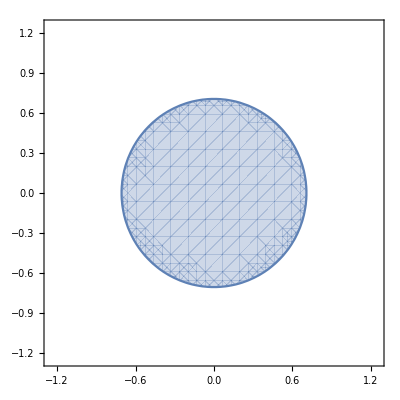

```mathematica
RegionPlot[x^2+y^2<(1/2),{x,-1.25,1.25},{y,-1.25,1.25}]
```

Use MTFNormalizedEqHor and choose a diameter of one in the inequality so as to make s_max equal to one as required by rule 2 above.

```mathematica
MTFNormalizedEqHor[x^2+y^2<(1/2)^2,{x,y}, fn]//Simplify
```

Piecewise[{{(-2 fn √(1-fn^2)+2 ArcCos[fn])/π, 0≤fn<1}, {0, True}}]

The normalized MTF in the horizontal direction is given by

(4)		Piecewise[{{(-2 fn √(1-fn^2)+2 ArcCos[fn])/π, 0≤fn<1}, {0, True}}]

### Square Entrance Pupil

-Graphics-
Figure 3.  Square entrance pupil with side a.

Use MTFNormalizedEqHor to find the equation for the MTF of a square entrance pupil and choose the length of a side to be equal to one so as to make s_max equal to one as required by rule 2 above.

```mathematica
MTFNormalizedEqHor[Abs[x]<1/2 && Abs[y]<1/2,{x,y}, fn ]
```

Piecewise[{{1-fn, 0≤fn<1}, {0, True}}]

The normalized MTF in the horizontal or vertical direction is

(5)		Piecewise[{{1-fn, 0≤fn<1}, {0, True}}]

### Semi-Circular Aperture

-Graphics-
Figure 4. Semi-circular entrance pupil with diameter D_0.

Use MTFNormalizedEqHor to find the equation for the MTF of the semi-circular pupil and choose the diameter to be equal to one so  s_max equals one in the horizontal direction as required by rule 2 above

```mathematica
MTFNormalizedEqHor[x^2 + y^2 <(1/2)^2&& y>0, {x,y},fn]//Simplify
```

Piecewise[{{(-2 fn √(1-fn^2)+2 ArcCos[fn])/π, 0≤fn<1}, {0, True}}]

The normalized MTF in the horizontal direction for the semicircular aperture is 

(6)		Piecewise[{{(-2 fn √(1-fn^2)+2 ArcCos[fn])/π, 0≤fn<1}, {0, True}}]

To find the MTF in the vertical direction, use MTFNormalizedEqVer and choose the diameter equal to two so as to make s_max equal to one in the vertical direction.

```mathematica
MTFNormalizedEqVer[x^2+y^2<1^2 && y>0,{x,y}, fn]
```

(2 (Piecewise[{{-fn √(1-fn^2)+ArcCos[fn], 0≤fn<1}, {0, True}}]))/π

The normalized MTF for the semicircular aperture in the vertical direction is

(7)		2/π (Piecewise[{{-fn √(1-fn^2)+ArcCos[fn], 0≤fn<1}, {0, True}}])

In Eq 7 the optical cutoff frequency f_OCO is given by D_0/(2λ).

Equations in Section 3 demonstrate that Mathematica reproduces known results.

## 4. Verification

This section uses several examples to illustrate the use of code given in Section 2 and to validate results produced by that code.

### Circular Entrance Pupil

Equation 4 is a well-known expression.  Evidence that NMTFNormalizedHor is correct is obtained by comparing the output of

```mathematica
temp = NMTFNormalizedHor[x^2+y^2<(1/2)^2,{x,y},30.];
```

with Eq. 4.

```mathematica
Show[{Plot[Piecewise[{{(-2 fn √(1-fn^2)+2 ArcCos[fn])/π, 0≤fn<1}, {0, True}}],{fn,0,1},Frame-> True, FrameLabel-> {{"MTF",""},{"f_n","Horizontal and Vertical MTF of Circular Entrance Pupil"}}, PlotLegends-> {"Analytical"}],ListPlot[temp, PlotStyle->PointSize[.02],PlotLegends-> {"Numerical"}] }]
```

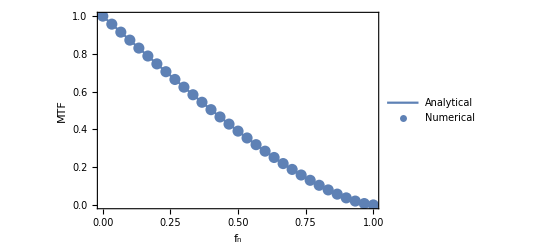
-Graphics-
Figure 5. Comparison of numerical and analytical calculations for circular entrance pupil.

### Square Entrance Pupil

Equation 5 is a well-known expression.  Gain additional evidence  NMTFNormalizedHor is correct by comparing its output with the results of Eq. 5.

```mathematica
temp = NMTFNormalizedHor[Abs[x]<1/2 && Abs[y] <1/2,{x,y},30.];
```

```mathematica
Show[{Plot[Piecewise[{{1-fn, 0≤fn<1}, {0, True}}],{fn,0,1},Frame-> True, FrameLabel-> {{"MTF",""},{"f_n","Horizontal and Vertical MTF of Square Entrance Pupil"}}, PlotLegends-> {"Analytical"}],ListPlot[temp, PlotStyle->PointSize[.02],PlotLegends-> {"Numerical"}] }]
```

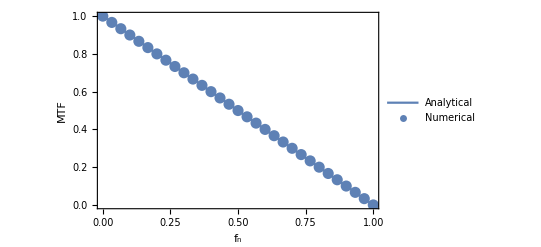
-Graphics-
Figure 6. Comparison of numerical and analytical calculations for a square entrance pupil

### Semi-circular aperture

Use NMTFNormalizedHor to gain confidence in this function and MTFNOrmalizedEqHor by determining if they are consistent.  The command used to generate numerical results is

```mathematica
temp = NMTFNormalizedHor[x^2+y^2<(1/2)^2&& y>0, {x,y},30.];
```

```mathematica
Show[{Plot[Piecewise[{{(-2 fn √(1-fn^2)+2 ArcCos[fn])/π, 0≤fn<1}, {0, True}}],{fn,0,1},Frame-> True, FrameLabel-> {{"MTF",""},{"f_n","Horizontal MTF of Semi-circular Pupil"}}, PlotLegends-> {"Analytical"}], ListPlot[temp, PlotStyle->PointSize[.02],PlotLegends-> {"Numerical"}]}]
```

-Graphics-
Figure 7. Comparison of numerical and analytical calculations for a semi-circular entrance pupil.

The above calculations served to verify MTFNormalizedEqHor and NMTFNormalizedEqHor.  Subsequent calculations will verify MTFCyclesPerMmEqHor and NTFCyclesPerMmHor.  When the output is given in cycles per mm, besides specifying the entrance pupil size it is necessary to also specify the wavelength of the incident radiation λ and the optical system focal length fl.  The calculations given below are for λ=10 μ and fl=10 mm.

### Elliptical Entrance Pupil

-Graphics-
Figure 8. Elliptical entrance pupil with minor axis of 5.0 mm and minor axis of 2.5 mm and the focal length of the lens is 10 mm.

Figure 8 was constructed using Mathematica’s drawing tools.  The entrance pupil shape is shown more accurately using RegionPlot.

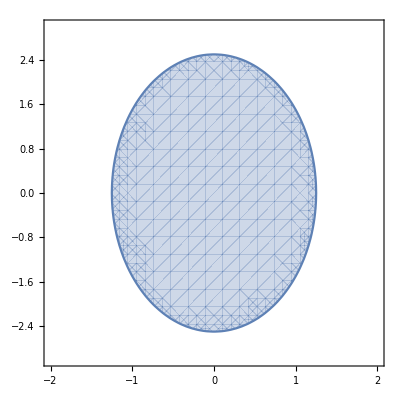

```mathematica
RegionPlot[(x/1.25)^2+(y/2.5)^2<1,{x,-2,2},{y,-3,3}]
```

Calculate the MTF in the horizontal and vertical directions for the entrance pupil illustrated in Fig. 8 for the case where the average wavelength of the incident radiation is 10 μ and the focal length is 10 mm.

```mathematica
temp1 = MTFCyclesPerMmEqHor [(x/1.25)^2+(y/2.5)^2<1,{x,y},10,10,f]; (* Analytical Calculation *)
```

```mathematica
temp2 = NMTFCyclesPerMmHor[(x/1.25)^2+(y/2.5)^2<1,{x,y},10,10,2.5,30.]; (* Numerical Calculation *)
```

```mathematica
temp3 = MTFCyclesPerMmEqVer[(x/1.25)^2+(y/2.5)^2<1,{x,y},10,10,f]; (* Analytical Calculation *)
```

```mathematica
temp4=NMTFCyclesPerMmVer[(x/1.25)^2+(y/2.5)^2<1,{x,y},10,10,5.0,30.]; (* Numerical Calculation *)
```

Exhibit the equation and numerical MTF results in the horizontal direction

```mathematica
temp1
```

0.101859 (Piecewise[{{9.81748, f/10==0.}, {0.25 (-0.2 f √(25.-0.04 f^2)+25. ArcCos[0.04 f]), 0.<f/10<2.5}, {0., True}}])

```mathematica
temp2
```

{{0,1.},{0.833333,0.957567},{1.66667,0.91518},{2.5,0.872889},{3.33333,0.830739},{4.16667,0.78878},{5.,0.74706},{5.83333,0.705629},{6.66667,0.664538},{7.5,0.623838},{8.33333,0.583583},{9.16667,0.543828},{10.,0.504632},{10.8333,0.466053},{11.6667,0.428154},{12.5,0.391002},{13.3333,0.354668},{14.1667,0.319226},{15.,0.284757},{15.8333,0.25135},{16.6667,0.219102},{17.5,0.18812},{18.3333,0.158527},{19.1667,0.130461},{20.,0.104088},{20.8333,0.079605},{21.6667,0.0572611},{22.5,0.0373861},{23.3333,0.0204553},{24.1667,0.0072689},{25.,0}}

Graph the equation for the MTF in the horizontal direction and compare with numerical results

```mathematica
Show[{Plot[temp1,{f,0,25},Frame-> True, FrameLabel-> {{"MTF",""},{"f [cycles/mm]","Horizontal MTF for Elliptical Entrance Pupil"}}, PlotLegends-> {"Analytical"}, ImageSize-> Large],ListPlot[temp2,PlotLegends-> {"Numerical"}] }]
```

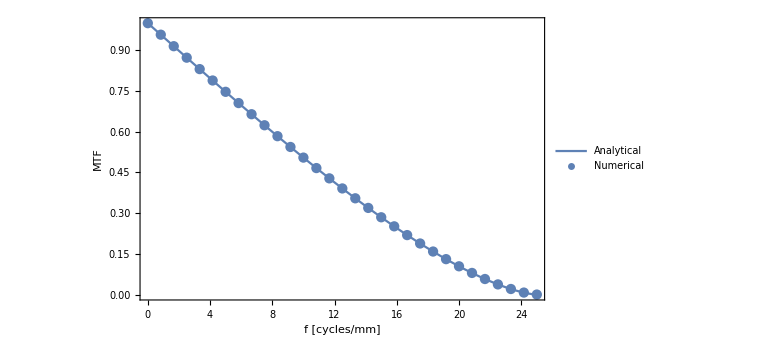
-Graphics-
Figure 9a.Comparison of numerical and analytical horizontal MTF calculations for entrance pupil of Fig.8.

Graph the equation for the MTF in the vertical direction and compare with numerical results

```mathematica
Show[{Plot[temp3,{f,0,50},Frame-> True, FrameLabel-> {{"MTF",""},{"f [cycles/mm]","Vertical MTF for Elliptical Entrance Pupil"}}, PlotLegends-> {"Analytical"}, ImageSize-> Large],ListPlot[temp4,PlotLegends-> {"Numerical"}] }]
```

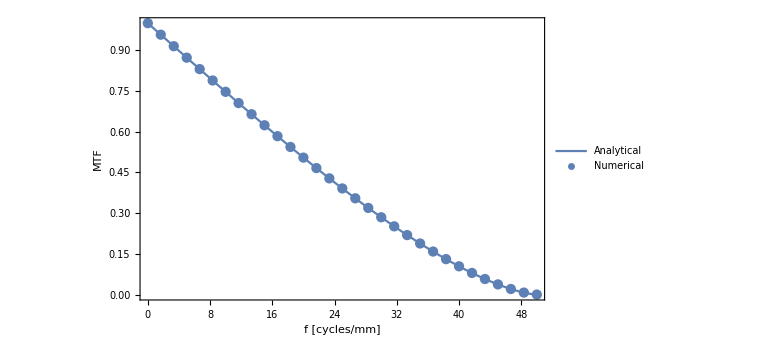
-Graphics-
Figure 9b.Comparison of numerical and analytical vertical MTF calculations for entrance pupil of Fig.8.

### Distributed Entrance Pupil

-Graphics-
				Figure 10. Distributed aperture.

Figure 10 was constructed using Mathematica’s drawing tools and Paint.  In Fig. 10 the center-to-center distance in the vertical and horizontal directions is 3.8 mm and each of the four clear areas has a diameter of 1.2 mm.

By symmetry, the MTF in the vertical and horizontal directions are the same.  Commands used to define the distributed aperture, RegionEntiree, are given below.

```mathematica
Region1 = x^2+ (y-1.9)^2<0.6^2;
Region2= x^2+ (y+1.9)^2<0.6^2;
Region3 = (x-1.9)^2+y^2<0.6^2;
Region4= (x+1.9)^2+y^2<0.6^2;
RegionEntire = Region1|| Region2|| Region3||Region4;
```

The shape of the distributed pupil is shown more accurately using RegionPlot

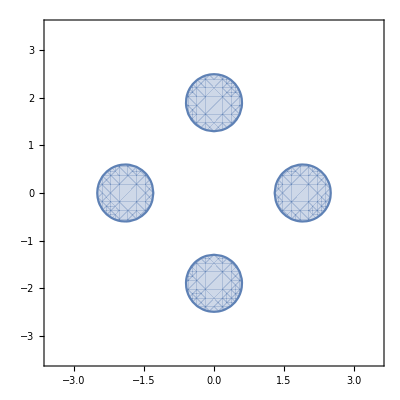

```mathematica
RegionPlot[RegionEntire,{x,-3.5,3.5},{y,-3.5,3.5}]
```

Commands used to generate the equation and table that define the horizontal or vertical MTF are given below for the case where λ=10 μ and fl=10 mm

```mathematica
temp1 =MTFCyclesPerMmEqVer[RegionEntire, {x,y},10,10,f];
```

```mathematica
temp2 = NMTFCyclesPerMmVer[RegionEntire,{x,y},10,10, 5,30];
```

Exhibit temp1 and temp2

```mathematica
temp1
```

0.221049 (Piecewise[{{-0.08 (0.5 f √(36.-0.25 f^2)-18. ArcCsc[6./(√(36.-0.25 f^2))]-18. ArcSin[0.166667 √(36.-0.25 f^2)]), 0.≤f/10<1.2}, {0.02 (42.4853 √(-65.+3.8 f-0.05 f^2)-1.11803 f √(-65.+3.8 f-0.05 f^2)+36. ArcSin[0.372678 √(-65.+3.8 f-0.05 f^2)]), 3.8<f/10<5.}, {0.02 (-42.4853 √(-65.+3.8 f-0.05 f^2)+1.11803 f √(-65.+3.8 f-0.05 f^2)+36. ArcSin[0.372678 √(-65.+3.8 f-0.05 f^2)]), 2.6<f/10≤3.8}, {0., True}}])

```mathematica
temp2
```

{{0,1.},{5/3,0.823731},{10/3,0.650925},{5,0.485261},{20/3,0.330936},{25/3,0.193191},{10,0.079605},{35/3,0.00553429},{40/3,0},{15,0},{50/3,0},{55/3,0},{20,0},{65/3,0},{70/3,0},{25,0},{80/3,0.00389684},{85/3,0.0249676},{30,0.0547755},{95/3,0.0901659},{100/3,0.129408},{35,0.171259},{110/3,0.214705},{115/3,0.241159},{40,0.197195},{125/3,0.154274},{130/3,0.113335},{45,0.0754661},{140/3,0.0420572},{145/3,0.015206},{50,0}}

The equation stored in temp1 is an original result.  Graph  the MTF in the horizontal or vertical direction for the distributed aperture shown in Fig. 10

```mathematica
Show[{Plot[temp1,{f,0, 50}, PlotRange-> All, Frame-> True, FrameLabel-> {{"MTF",""},{"f [cycles/mm]","Horizontal or Vertical MTF for Distibuted Aperture"}}, PlotLegends-> {"Analytical"}, ImageSize-> Large], ListPlot[temp2, PlotRange-> All, PlotLegends-> {"Numerical"}]}]
```

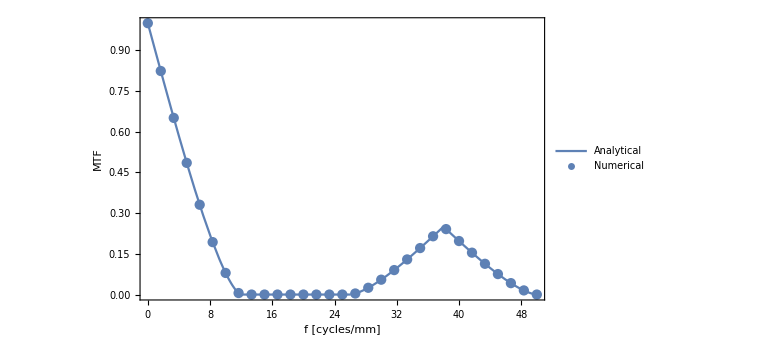
-Graphics-
Figure 11.  Compaarison of numerical and analytical calculations for the distributed aperture of Fig. 10.

### Racetrack Aperture

The racetrack aperture is defined by RegionEntire and is graphed using RegionPlot.

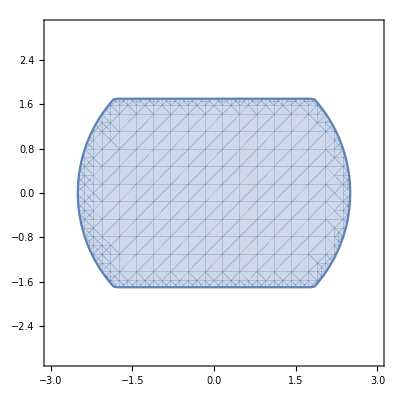

```mathematica
RegionEntire = x^2+y^2<2.5^2 &&Abs[y]<1.7; RegionPlot[RegionEntire,{x,-3,3},{y,-3,3}]
```

Figure 12 was drawn by pasting the above RegionPlot into Paint, inserting the dimensions and lines using paint and the arrows using Mathematica.

-Graphics-
	Figure 12.  Racetrack aperture.

In Fig. 12 a clear circular entrance pupil 5.0 mm in diameter is truncated to be 3.4 mm in the vertical direction.  The following commands output the equations and numerical tables for the horizontal and vertical MTF for a system with an average wavelength of 10 μ and a focal length of 10 mm.

```mathematica
temp1 = MTFCyclesPerMmEqHor[x^2+y^2<2.5^2 && Abs[y]<1.7, {x,y}, 10,10,f];
temp2 = MTFCyclesPerMmEqVer[x^2+y^2<2.5^2 && Abs[y]<1.7, {x,y}, 10,10,f];
temp3 = NMTFCyclesPerMmHor[x^2+y^2<2.5^2 && Abs[y]<1.7, {x,y}, 10,10, 5.0,25.];
temp4 =  NMTFCyclesPerMmVer[x^2+y^2<2.5^2 && Abs[y]<1.7, {x,y}, 10,10, 3.4,25.];
```

Exhibit the MTF equation and numerical data which describes the horizontal MTF for the racetrack aperture shown in Fig. 12 and graph the data

```mathematica
temp1
```

0.0641876 (Piecewise[{{3.11473, f/10==3.66606}, {15.5793, f/10==0.}, {0.02 (778.967-17. f), 0.<f/10<3.66606}, {1.12508, f/10==4.33303}, {0.5 (-0.1 f √(25.-0.01 f^2)+25. ArcCos[0.02 f]), 3.66606<f/10<4.33303||4.33303<f/10<5.}, {0., True}}])

```mathematica
temp3
```

{{0,1.},{2.,0.956352},{4.,0.912705},{6.,0.869057},{8.,0.82541},{10.,0.781762},{12.,0.738115},{14.,0.694467},{16.,0.65082},{18.,0.607172},{20.,0.563524},{22.,0.519877},{24.,0.476229},{26.,0.432582},{28.,0.388934},{30.,0.345287},{32.,0.301639},{34.,0.257991},{36.,0.214344},{38.,0.171334},{40.,0.131184},{42.,0.0944685},{44.,0.0617463},{46.,0.0338196},{48.,0.0120304},{50.,0}}

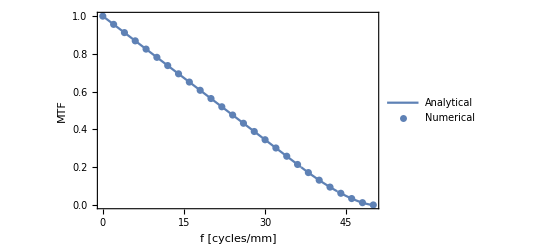

```mathematica
Show[{Plot[temp1, {f,0,50}, Frame-> True, FrameLabel-> {{"MTF",""},{"f [cycles/mm]","Horizontal MTF for Racetrack Entrance Pupil"}}, PlotLegends-> {"Analytical"}],ListPlot[temp3, PlotLegends-> {"Numerical"}]}]
```

Similarly, the vertical racetrack MTF is displayed

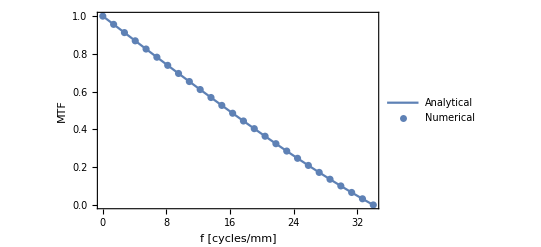

```mathematica
Show[{Plot[temp2, {f,0,34}, Frame-> True, FrameLabel-> {{"MTF",""},{"f [cycles/mm]","Vertical MTF for Racetrack Entrance Pupil"}}, PlotLegends-> {"Analytical"}],ListPlot[temp4, PlotLegends-> {"Numerical"}]}]
```

## 5. Summary and Conclusions

In this paper, functions have been written in Mathematica that take as input the shape and size of the entrance pupil and output either analytically or numerically incoherent optical MTF functions.  Although CODEV, ZEMAX and other programs can numerically calculate these incoherent optical MTFs I am not aware of any other program that can take as input an analytical expression of the input pupil and output an analytical MTF in the specified direction.  If an exact description of the entrance pupil is input, then code exhibited here that produces analytical results output an exact expression for the MTF in the specified direction.

Functions exhibited here has been verified with several entrance pupil shapes by comparing Mathematica generated analytical and numerical expressions against themselves and with numerical calculations done by CODEV.

For a sufficiently complicated entrance pupil description, functions exhibited here that produce an analytical result may grind on endlessly and fail to produce an analytical result.  For an entrance pupil that has sufficiently fine detail, functions exhibited here that produce a numerical result may need tweaking to properly reflect changes in the MTF caused by fine detail.

This notebook demonstrates computer programs that programs that produce analytical MTF results for cases where it is either too hard or too tedious to get analytical results by hand calculations.  This notebook can serve as a user’s manual for the functions given in Section 2.